```mathematica
NS[]
```

```mathematica
solgamma=FS@Solve[{mode==(a-1)*b,var==a*b^2},{a,b}][[2]]
```

{a→1+(mode (mode+√(mode^2+4 var)))/(2 var),b→1/2 (-mode+√(mode^2+4 var))}

```mathematica
pdfg[x_,mode_,var_]=Assuming[x>0,FS[PDF[GammaDistribution[a,b],x]/.solgamma]]
```

(2^(1+(mode (mode+√(mode^2+4 var)))/(2 var)) ⅇ^((2 x)/(mode-√(mode^2+4 var))) ((-mode+√(mode^2+4 var))/x)^(-1-(mode (mode+√(mode^2+4 var)))/(2 var)))/(x Gamma[1+(mode (mode+√(mode^2+4 var)))/(2 var)])

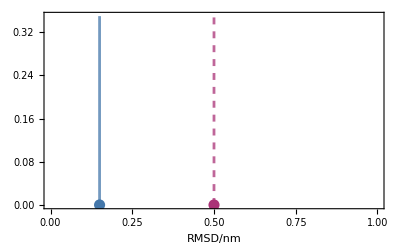

```mathematica
plotmodes=ListPlot[{{{0.15,0},{0.15,0.35}},{{0.5,0},{0.5,0.35}}},Joined->True,BaseStyle->Directive[Thickness[0.005],Opacity[0.75]],PlotStyle->{purpleblue,redpurple},PlotRange->{{0,1},{All,0.35}},FrameLabel->{"RMSD/nm",None},Epilog->{{PointSize[0.02],purpleblue,Point[{0.15,0}]},{PointSize[0.02],redpurple,Point[{0.5,0}]}}]
```

```mathematica
expng["candiditesmodes",plotmodes]
```

candiditesmodes.png

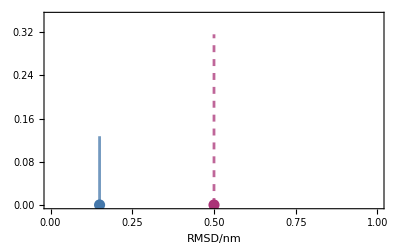

```mathematica
plotmodes2=ListPlot[{{{0.15,0},{0.15,pdfg[0.15*10,1.5,25]}},{{0.5,0},{0.5,(1-rat)*pdfg[0.5*10,5,0.2]+rat*pdfg[0.5*10,1,5]}}},Joined->True,BaseStyle->Directive[Thickness[0.005],Opacity[0.75]],PlotStyle->{purpleblue,redpurple},PlotRange->{{0,1},{All,0.35}},FrameLabel->{"RMSD/nm",None},Epilog->{{PointSize[0.02],purpleblue,Point[{0.15,0}]},{PointSize[0.02],redpurple,Point[{0.5,0}]}}]
```

```mathematica
rat=0.7;
```

General::munfl: 1/388.525^126.992 is too small to represent as a normalized machine number; precision may be lost.

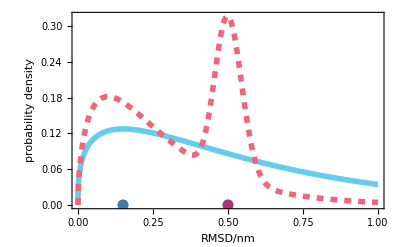

```mathematica
plot=Plot[{pdfg[x*10,1.5,25],(1-rat)*pdfg[x*10,5,0.2]+rat*pdfg[x*10,1,5]},{x,0,1},PlotRange->{{0,1},{All,0.35}},PlotStyle->Directive[Thickness[0.01]],FrameLabel->{"RMSD/nm","probability density"},Epilog->{{PointSize[0.02],purpleblue,Point[{0.15,0}]},{PointSize[0.02],redpurple,Point[{0.5,0}]}}]
```

```mathematica
expng["candiditespdfs",plot]
```

candiditespdfs.png

```mathematica
Integrate[pdfg[x,1.5,25],{x,0,2.5}]
```

0.290005

```mathematica
Integrate[(1-rat)*pdfg[x,5,0.2]+rat*pdfg[x,1,5],{x,0,2.5}]
```

0.388118

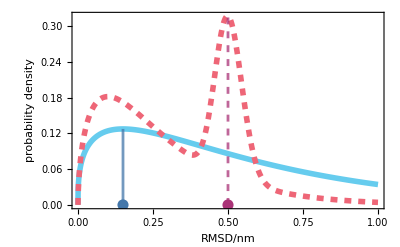

```mathematica
plotjoint=Show[{plot,plotmodes2}]
```

```mathematica
expng["candiditespdfs2",plotjoint]
```

candiditespdfs2.png

```mathematica
cost1={{10,-5},{0,0}};cost2={{10,-1},{0,0}};

pr1={a1,1-a1};pr2={a2,1-a2};
FS@{cost1.pr1,cost2.pr2}
```

{{-5+15 a1,0},{-1+11 a2,0}}

```mathematica
Reduce[((cost1.pr1)[[1]]<(cost2.pr2)[[1]])/.(a1->0.6)]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

a2>0.454545

```mathematica
cost1={{8,-2},{0,0}};cost2={{9,-0.95},{0,0}};

pr1={a1,1-a1};pr2={a2,1-a2};
FS@{cost1.pr1,cost2.pr2}
```

{{-2+10 a1,0},{-0.95+9.95 a2,0}}

```mathematica
Reduce[((cost1.pr1)[[1]]<(cost2.pr2)[[1]])/.(a1->0.55)]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

a2>0.447236

```mathematica
FS@{cost1.pr1,cost2.pr2}/.{a1->0.55,a2->0.45}
```

{{3.5,0},{3.5275,0}}

```mathematica
pdf[x_,mus_,sis_,ws_]:=Sum[PDF[NormalDistribution[mus[[i]],sis[[i]]],x]*ws[[i]],{i,Length[ws]}];
```

```mathematica
nn=100;
mus=RandomVariate[NormalDistribution[5,5],nn];
sis=Exp@RandomVariate[NormalDistribution[0,1],nn];
ws=(#/Total[#])&@RandomReal[{0,1},nn];
```

```mathematica
genpdf[x_,nn_,mu0_,si0_,sic0_]:=Module[{mus,sis,ws},
mus=RandomVariate[NormalDistribution[mu0,si0],nn];
sis=Exp@RandomVariate[NormalDistribution[sic0,0.5],nn];
ws=(#/Total[#])&@RandomReal[{0,1},nn];
pdf[x,mus,sis,ws]];
```

```mathematica
f[x_]=genpdf[x,10,0,5,0];
```

General::munfl: Exp[-958.805] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-779.299] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-953.364] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-2100.68] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-911.013] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2029.32] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

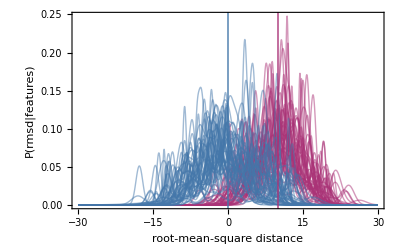

```mathematica
tabf=Table[genpdf[x,20,0,6,0],50];plotblue=Plot[tabf,{x,-30,30},PlotRange->All,PlotStyle->Directive[Thin,solid,purpleblue,Opacity[0.5]],FrameTicks->None];

tabf=Table[genpdf[x,20,10,5,0],50];plotred=Plot[tabf,{x,-30,30},PlotRange->All,PlotStyle->Directive[Thin,solid,redpurple,Opacity[0.5]],FrameTicks->None,Epilog->{{Thick,purpleblue,InfiniteLine[{0,0},{0,1}]},{Thick,redpurple,InfiniteLine[{10,0},{0,1}]}},FrameLabel->{"root-mean-square distance","P"[rmsd|"features"]}];

totplot=Show[plotred,plotblue]
```

```mathematica
expng["wide",totplot]
```

wide.png

General::munfl: Exp[-797.107] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-992.889] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1025.22] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-2377.44] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2932.07] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5246.79] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

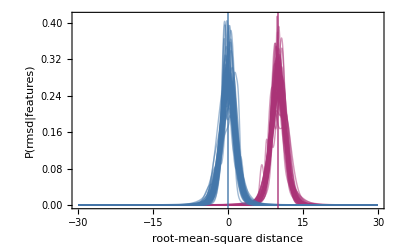

```mathematica
tabf=Table[genpdf[x,20,0,1,0],50];plotblue=Plot[tabf,{x,-30,30},PlotRange->All,PlotStyle->Directive[Thin,solid,purpleblue,Opacity[0.5]],FrameTicks->None];

tabf=Table[genpdf[x,20,10,1,0],50];plotred=Plot[tabf,{x,-30,30},PlotRange->All,PlotStyle->Directive[Thin,solid,redpurple,Opacity[0.5]],FrameTicks->None,Epilog->{{Thick,purpleblue,InfiniteLine[{0,0},{0,1}]},{Thick,redpurple,InfiniteLine[{10,0},{0,1}]}},FrameLabel->{"root-mean-square distance","P"[rmsd|"features"]}];

totplot=Show[plotred,plotblue]
```

```mathematica
expng["narrow",totplot]
```

narrow.png

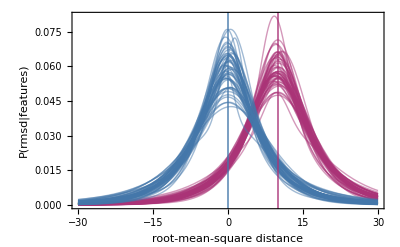

```mathematica
tabf=Table[genpdf[x,20,0,1,2],50];plotblue=Plot[tabf,{x,-30,30},PlotRange->All,PlotStyle->Directive[Thin,solid,purpleblue,Opacity[0.5]],FrameTicks->None];

tabf=Table[genpdf[x,20,10,1,2],50];plotred=Plot[tabf,{x,-30,30},PlotRange->All,PlotStyle->Directive[Thin,solid,redpurple,Opacity[0.5]],FrameTicks->None,Epilog->{{Thick,purpleblue,InfiniteLine[{0,0},{0,1}]},{Thick,redpurple,InfiniteLine[{10,0},{0,1}]}},FrameLabel->{"root-mean-square distance","P"[rmsd|"features"]}];

totplot=Show[plotred,plotblue]
```

```mathematica
expng["narrow_wide",totplot]
```

narrow_wide.png

General::munfl: Exp[-1194.67] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3958.79] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-735.795] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

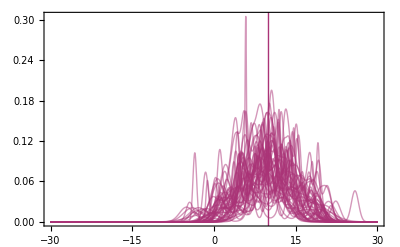

```mathematica
tabf=Table[genpdf[x,20,0,1,0],50];plotred=Plot[tabf,{x,-30,30},PlotRange->All,PlotStyle->Directive[Thin,solid,redpurple,Opacity[0.5]],FrameTicks->None,Epilog->{Thick,redpurple,InfiniteLine[{10,0},{0,1}]}]
```

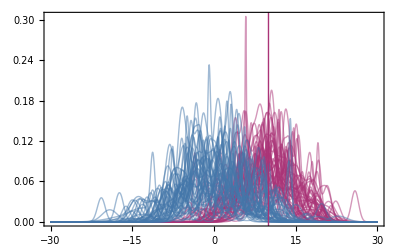

```mathematica
Show[plotred,plotblue]
```

```mathematica
tabf=Table[genpdf[x,20,10,5,0],50];
```

General::munfl: Exp[-1461.24] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1167.41] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3208.22] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

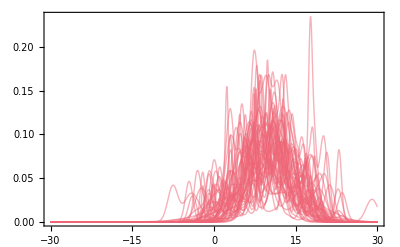

```mathematica
Plot[tabf,{x,-30,30},PlotRange->All,PlotStyle->Directive[Thin,solid,red,Opacity[0.5]],FrameTicks->None]
```

```mathematica
tabf=Table[genpdf[x,20,0,1,0],50];
```

General::munfl: Exp[-1592.46] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2473.52] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1129.78] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

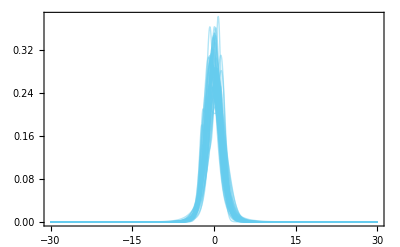

```mathematica
Plot[tabf,{x,-30,30},PlotRange->All,PlotStyle->Directive[Thin,solid,blue,Opacity[0.5]],FrameTicks->None]
```

```mathematica
tabf=Table[genpdf[x,20,10,1,0],50];
```

General::munfl: Exp[-3583.11] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-817.663] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-900.691] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

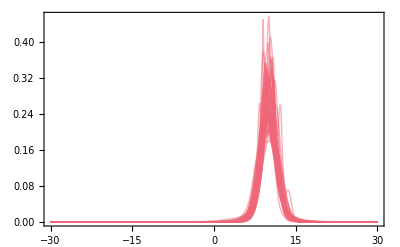

```mathematica
Plot[tabf,{x,-30,30},PlotRange->All,PlotStyle->Directive[Thin,solid,red,Opacity[0.5]],FrameTicks->None]
```